# Energy Acceptance and Beam Loss due to ICS

## Units, Constants and Parameters

```mathematica
(*Units*)
```

```mathematica
MeVc2=10^6;
nm=10^-9;
MeV=10^6;
GeV=10^9;
TeV=10^12;
```

```mathematica
(*Constants*)
me=0.51099895MeVc2;
c=299792458;
h=4.1357*10^-15; (*in eV s*)
```

```mathematica
(*Parameters*)
λ=1064nm;
```

## Intermediaries

```mathematica
EL[λ_]:=(h*c)/λ
```

## Maximum Required Energy Acceptance (non-recoil and recoil) Head-on

This is the energy acceptance required to keep all of the electrons after an ICS interaction. Recoil is neglected i.e the Thomson regime and the photon electron collision is head-on.

```mathematica
EacceptMAXnonrec[λ_,Ee_]:=(4*EL[λ]*(Ee^2+2*Ee*me+me^2))/(Ee*me^2);
```

This is the energy acceptance required to keep all of the electrons after an ICS interaction with recoil effect took into account. This is still for a head-on collision.

```mathematica
EacceptMAXrec[λ_,Ee_]:=(4*EL[λ]*(Ee^2+2*Ee*me+me^2))/(Ee*me^2*(1+(4*EL[λ]*(Ee+me))/me^2));
```

Note here that Ee is the kinetic energy of the electron. This could be extended to none head-on collisions fairly easily.

## Plotting EacceptMAX vs Ee

```mathematica
acceptnonrec=Table[{Ee/MeV,EacceptMAXnonrec[λ,Ee]},{Ee,MeV,10GeV,MeV}];
```

```mathematica
acceptrec=Table[{Ee/MeV,EacceptMAXrec[λ,Ee]},{Ee,MeV,10GeV,MeV}];
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

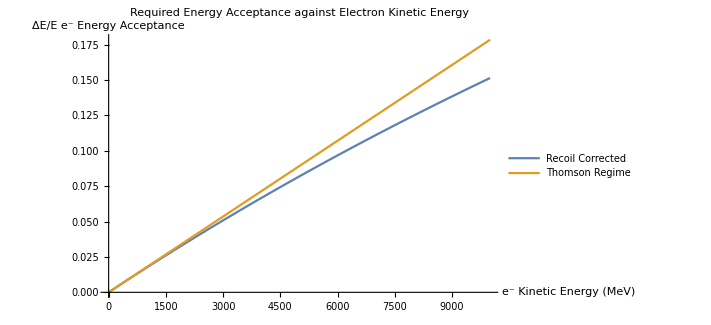

```mathematica
ListLinePlot[{acceptrec,acceptnonrec},PlotLabel->"Required Energy Acceptance against Electron Kinetic Energy",AxesLabel->{"e^- Kinetic Energy (MeV)","ΔE/E e^- Energy Acceptance"},PlotLegends->Placed[{"Recoil Corrected","Thomson Regime"},{0.8,0.2}]]
```

```mathematica
DIANAdat={{340,EacceptMAXrec[λ,340MeV]},{680,EacceptMAXrec[λ,680MeV]},{1020,EacceptMAXrec[λ,1020MeV]}};
CBETAdat={{42,EacceptMAXrec[λ,42MeV]},{78,EacceptMAXrec[λ,78MeV]},{114,EacceptMAXrec[λ,114MeV]},{150,EacceptMAXrec[λ,150MeV]}};
```

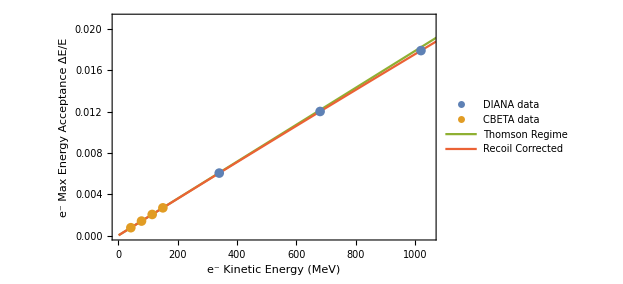

```mathematica
ListPlot[{DIANAdat,CBETAdat,acceptnonrec,acceptrec},Joined->{False,False,True,True},Frame->True,LabelStyle->15,FrameLabel->{"e^- Kinetic Energy (MeV)","e^- Max Energy Acceptance ΔE/E "},PlotLegends->Placed[LineLegend[{"DIANA data","CBETA data","Thomson Regime","Recoil Corrected"},LabelStyle->12,LegendFunction->frame],{0.75,0.25}],PlotRange->{{0,1050},{0,0.021}},PlotStyle->PointSize[0.015]]
```